# Basic Usage

This Tech Note introduces the functionality of the HyperBloch package. The package provides an interface for dealing with hyperbolic cell graphs such as those produced by the HyperCells GAP package, visualizing the graphs and their properties, defining tight-binding models on hyperbolic lattices, and constructing (Abelian) Bloch Hamiltonians.

This loads the package:

```mathematica
Needs["PatrickMLenggenhager`HyperBloch`"]
```

## Import of Cell Graphs

The HyperCells GAP package produces three different types of output: cell graph, model graphs, and supercell model graphs. The corresponding text files, typically with extensions *.hcc, *.hcm, and *.hcs, respectively, can be imported using the following three import functions.

ImportCellGraphString["string"] | import a cell graph from a string in the HCC format
ImportModelGraphString["string"] | import a model graph from a string in the HCM format
ImportSupercellModelGraphString["string"] | import a supercell model graph from a string in the HCS format

Import of cell, model, and supercell model graphs.

The cell graphs are returned as objects with head HCCellGraph, HCModelGraph, and HCSupercellModelGraph, respectively. See the corresponding documentation for a description of their properties.

Import a cell graph from a *.hcc file and extract some of its basic properties.

```mathematica
(cellgraphT26=ImportCellGraphString[Import["PatrickMLenggenhager/HyperBloch/ExampleData/(2,8,8)_T2.6_3.hcc"]])//Head
```

HCCellGraph

```mathematica
cellgraphT26["TriangleGroup"]
```

{2,8,8}

```mathematica
cellgraphT26["CellCenter"]
```

3

```mathematica
cellgraphT26["Genus"]
```

2

Import a model graph from a *.hcm file and extract some of its basic properties.

```mathematica
(modelgraphT26=ImportModelGraphString[Import["PatrickMLenggenhager/HyperBloch/ExampleData/{8,8}-tess_T2.6_3.hcm"]])//Head
```

HCModelGraph

```mathematica
modelgraphT26["TriangleGroup"]
```

{2,8,8}

```mathematica
modelgraphT26["CellCenter"]
```

3

```mathematica
modelgraphT26["Genus"]
```

2

Import a supercell model graph from a *.hcs file and extract some of its basic properties.

```mathematica
(scmodelgraphT311=ImportSupercellModelGraphString[Import["PatrickMLenggenhager/HyperBloch/ExampleData/{8,8}-tess_T2.6_3_sc-T3.11.hcs"]])//Head
```

HCSupercellModelGraph

```mathematica
scmodelgraphT311["PCGenus"]
```

2

```mathematica
scmodelgraphT311["Genus"]
```

3

Other properties such as the graph itself, edge translations, boundary identifications, and faces can be extracted similarly.

Import a model graph from a *.hcm file and extract the graph and faces as Graph objects.

```mathematica
modelgraphT21=ImportModelGraphString[Import["PatrickMLenggenhager/HyperBloch/ExampleData/{8,3}-tess_T2.1_3.hcm"]];
```

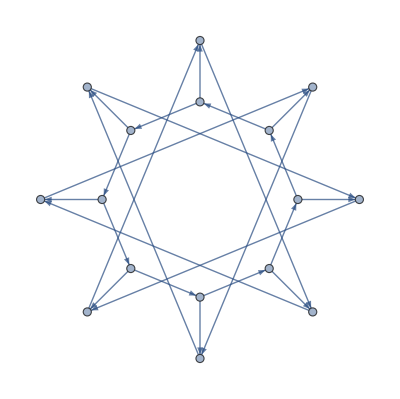

```mathematica
modelgraphT21["Graph"]
```

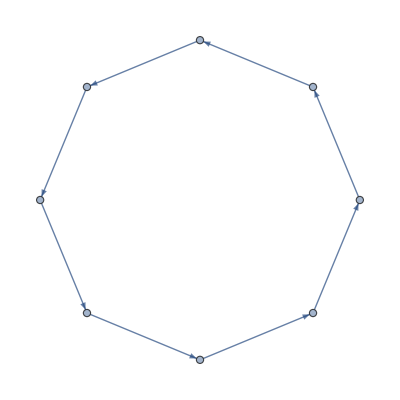
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
Row@modelgraphT21["Faces"]
```

For visualization purposes it is usually more convenient to use the built-in visualization functions taking cell, model, and supercell model graphs as input. These are described below.

## Visualization of Cell Graphs

Cell graphs, including (supercell) model graphs, are visualized in the Poincaré disk. The HyperBloch package provides two high-level visualization functions which can show the various elements stored in the HCCellGraph, HCModelGraph, and HCSupercellModelGraph objects.

VisualizeCellGraph[cgraph] | visualize the HCCellGraph cgraph and its properties in the Poincaré disk
VisualizeModelGraph[cgraph] | visualize the HCModelGraph cgraph or HCSupercellModelGraph and its properties in the Poincaré disk

High-level visualization functions for cell, model, and supercell model graphs.

For both, the option Elements specifies which elements of the cell or model graph are shown and allows options for those to be passed to the corresponding lower-level visualization functions (see the corresponding reference page of the function). The following elements are available.

ShowCellBoundary | boundary of the cell, including the boundary edge identification (in VisualizeModelGraph this requires the CellGraph option to be set to an appropriate HCCellGraph)
ShowCellGraph | compactified cell graph
ShowCellGraphFlattened | flattened cell graph
ShowCellSchwarzTriangles | Schwarz triangles making up the cell

Elements available for visualization.

Additionally, options of ShowTriangles, Graphics, and Rasterize can be given and are passed on.

Visualize a model graph with the default options.

```mathematica
VisualizeModelGraph[modelgraphT21,ImageSize->300]
```

-Graphics-

Show the compactified graph instead and display more triangles.

```mathematica
VisualizeModelGraph[modelgraphT21,
Elements-><|
ShowCellGraph->{}
|>,
NumberOfGenerations->3,
ImageSize->300]
```

-Graphics-

Show the boundary identification stored in the corresponding cell graph.

```mathematica
cellgraphT21=ImportCellGraphString[Import["PatrickMLenggenhager/HyperBloch/ExampleData/(2,3,8)_T2.1_3.hcc"]];
```

```mathematica
VisualizeModelGraph[modelgraphT21,
Elements-><|
ShowCellGraphFlattened->{},
ShowCellBoundary->{ShowEdgeIdentification->True}
|>,
CellGraph->cellgraphT21,
NumberOfGenerations->3,
ImageSize->300]
```

-Graphics-

### Vertices, Edges, Faces

Instead of visualizing the full cell graph, its elements, i.e., vertices, edges, faces, can be constructed separately using the following functions. These functions can be applied to HCCellGraph, HCModelGraph, and HCSupercellModelGraph objects.

GetCellGraphVertex[cgraph,vertex] | construct a Point representing the position of vertex in cgraph
GetCellGraphEdge[cgraph,edge] | construct a Line representing edge of cgraph
GetCellGraphFace[cgraph, face]  | construct a Polygon and list of Arrows representing face of cgraph

Functions for visualizing vertices, edges, and faces of  HCCellGraph, HCModelGraph, and HCSupercellModelGraph objects.

In order to show those Graphics elements, it is convenient to use the ShowTriangles function which displays the triangle-tessellation pertaining to a given triangle group in the Poincaré disk.

ShowTriangles[tg] | constructs the Schwarz triangles of the triangle group with signature tg in the Poincaré disk representation

Visualization of the triangle-tessellation pertaining to a triangle group.

RasterizeGraphics | True | whether to rasterize the triangle graphics
NumberOfGenerations | 2 | number of generations of triangles to construct
DiskCenter | 3 | type of vertex to center the disk at, integer between 1 and 3 corresponding to x, y, z
ColorFill | LightGray | color for filling the triangles
ColorBoundary | RGBColor[{0,0,0,0}] | color of the triangle boundary
LineThickness | 0 | thickness of the triangle boundary

Options for ShowTriangles.

Show a particular vertex of a model graph in the Poincaré disk.

```mathematica
VertexList[modelgraphT21["Graph"]]
```

{{2,1},{2,2},{2,3},{2,4},{2,5},{2,6},{2,7},{2,8},{2,9},{2,10},{2,11},{2,12},{2,13},{2,14},{2,15},{2,16}}

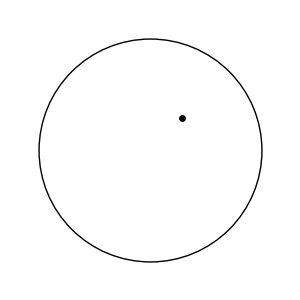

```mathematica
Show[
ShowTriangles[{2,3,8},NumberOfGenerations->3,ImageSize->300],
Graphics[{Black,AbsolutePointSize[5],
GetCellGraphVertex[modelgraphT21, {2,2}]
}]
]
```

Show a particular edge of a model graph in the Poincaré disk.

```mathematica
EdgeList[modelgraphT21["Graph"]]//Short
```

{{2,1}{2,2}{1,{1,1,9}},«22»,{2,15}{2,11}{1,{24,39,43}}}

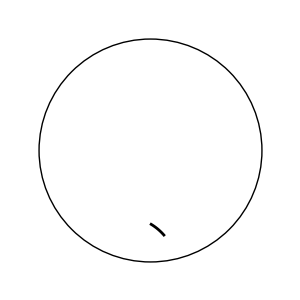

```mathematica
Show[
ShowTriangles[{2,3,8},NumberOfGenerations->3,ImageSize->300],
Graphics[{Black,AbsoluteThickness[2],
GetCellGraphEdge[modelgraphT21, {2,15}{2,11}{1,{24,39,43}}]
}]
]
```

Show a particular face of a model graph in the Poincaré disk.

```mathematica
face=modelgraphT21["Faces"][[6]]
```

-Graphics-

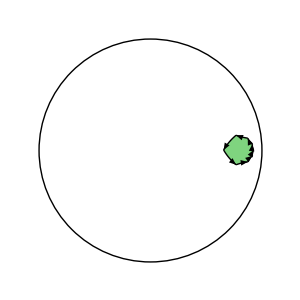

```mathematica
Show[
ShowTriangles[{2,3,8},NumberOfGenerations->3,ImageSize->300],
Graphics[{FaceForm[{Darker@Green,Opacity[0.5]}],Arrowheads[{{0.02,0.5}}],
GetCellGraphFace[modelgraphT21, face]
}]
]
```

### Cell Boundary

While the cell boundary is conveniently visualized using the ShowCellBoundary function, it can be useful to get the cell boundary as a collection of lines, labeled by their identification. This is achieved by the GetCellBoundary function.

GetCellBoundary[cgraph] | construct the cell boundary of the HCCellGraph cgraph

Constructing the cell boundary of a cell graph.

Construct the cell boundary of a cell graph.

```mathematica
GetCellBoundary[cellgraphT21]//Shallow
```

{{1,Line[«1»],Point[«1»],g1},{1,Line[«1»],Point[«1»],g1^-1},{2,Line[«1»],Point[«1»],g2},{2,Line[«1»],Point[«1»],g2^-1},{3,Line[«1»],Point[«1»],g3},{3,Line[«1»],Point[«1»],g3^-1},{4,Line[«1»],Point[«1»],g4},{4,Line[«1»],Point[«1»],g4^-1},{1,Line[«1»],Point[«1»],g1^-1},{1,Line[«1»],Point[«1»],g1},«22»}

## Low-Level Visualization Functions

Sometimes it is convenient to work directly with the triangle group instead of with the graphs. The elements g of the triangle group (given as words in the generators x,y,z) are in one-to-one correspondence with Schwarz triangles. For each Schwarz triangle, its vertices are maximally-symmetric Wyckoff positions, such that those are labeled by their type w (taking the values 1,2,3, selecting on of the three vertices of the triangle) and the label g of the triangle. The following functions are provided to construct Graphics elements relating to them.

GetSchwarzTriangle[tg,"g"] | construct a Polygon representing the Schwarz triangle specified by the element g of the triangle group tg
GetVertex[tg,{w,"g"}] | construct a Point representing the Wyckoff position of type w and label g of the triangle group tg
GetEdge[tg,{{w_1,"g_1"},{w_1,"g_2"},...}] | a Line representing the edge (or succession of edges) specified by vertices {w_i,"g_i"} of the triangle group tg

Functions returning Graphics elements representing a triangle group's Schwarz triangles, Wyckoff positions and geodesics between Wyckoff positions in the Poincaré disk.

Show a particular Schwarz triangle in the Poincaré disk.

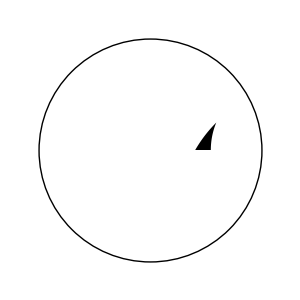

```mathematica
Show[
ShowTriangles[{2,3,8},NumberOfGenerations->3,ImageSize->300],
Graphics[{FaceForm[Black],GetSchwarzTriangle[{2,3,8},"z*x"]}]
]
```

Show a particular maximally-symmetric Wyckoff position in the Poincaré disk.

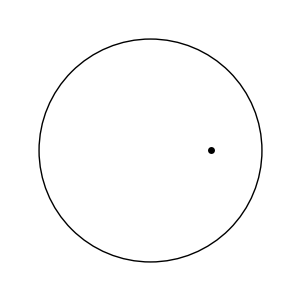

```mathematica
Show[
ShowTriangles[{2,3,8},NumberOfGenerations->3,ImageSize->300],
Graphics[{Black,AbsolutePointSize[5],GetVertex[{2,3,8},{1,"z*x"}]}]
]
```

Show a geodesic between several particular maximally-symmetric Wyckoff positions in the Poincaré disk.

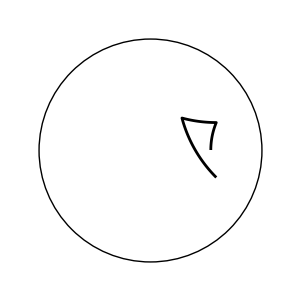

```mathematica
Show[
ShowTriangles[{2,3,8},NumberOfGenerations->3,ImageSize->300],
Graphics[{Black,AbsoluteThickness[2],
GetEdge[{2,3,8},{{1,"z*x"},{3,"x"},{2,"z"},{3,"y"}}]
}]
]
```

## Hyperbolic Band Theory

Hyperbolic band theory relies on block-diagonalizing the full Hamiltonian into blocks characterized by irreducible representations of a given translation group. Due to the translation group being non-Abelian, higher-dimensional irreducible representations exist.

### Abelian Bloch Hamiltonian

Focusing only on the one-dimensional irreducible representation, results in an approximation called Abelian hyperbolic band theory. The one-dimensional irreducible representations take an analogous form as in the Euclidean case, i.e., they take the form of Bloch phase factors with one independent momentum component k for each independent generator γ_i  of the translation group: e^(ⅈ k_i). This allows us to easily construct the Abelian Bloch Hamiltonian based on a (supercell) model graph.

AbelianBlochHamiltonianExpression[mgraph,norb,onsite,hoppings,k]  | construct the Abelian Bloch Hamiltonian ℋ(k) of the HCModelGraph or HCSupercellModelGraph mgraph with the number of orbitals at each site specified by norb, the onsite term by onsite, and the hopping along an edge by hoppings in terms of momenta k[i]
AbelianBlochHamiltonian[mgraph,norb,onsite,hoppings] | construct the Abelian Bloch Hamiltonian ℋ(k) of the HCModelGraph or HCSupercellModelGraph mgraph with the number of orbitals at each site specified by norb, the onsite term by onsite, and the hopping along an edge by hoppings as a function k :> ℋ(k)

Construction of Abelian Bloch Hamiltonians.

Obtain the Abelian Bloch Hamiltonian of the elementary nearest-neighbor hopping model on the {8,8} lattice (on the primitive cell T2.6).

```mathematica
FullSimplify@AbelianBlochHamiltonianExpression[modelgraphT26,1,0&,-1&,k][[1,1]]
```

-2 (Cos[k[1]]+Cos[k[2]]+Cos[k[3]]+Cos[k[4]])

Obtain the same as a function instead.

```mathematica
H=AbelianBlochHamiltonian[modelgraphT26,1,0&,-1&]
```

Function[{k1,k2,k3,k4},{{-ⅇ^(-ⅈ k1)-ⅇ^(ⅈ k1)-ⅇ^(-ⅈ k2)-ⅇ^(ⅈ k2)-ⅇ^(-ⅈ k3)-ⅇ^(ⅈ k3)-ⅇ^(-ⅈ k4)-ⅇ^(ⅈ k4)}}]

```mathematica
H[0,0,0,0]
```

{{-8}}

Both AbelianBlochHamiltonianExpression and AbelianBlochHamiltonian accept an HCModelGraph as option PCModel for defining norb, onsite, and hoppings on the corresponding primitive cell instead of on the supercell directly. This is useful for extending nontrivial models defined on the primitive cell to larger supercells.

Define a nearest-neighbor hopping model on the primitive cell T2.6 of the {8,8} lattice such that the hopping amplitude depends on the direction.

```mathematica
modelgraphT26["EdgeTranslations"]
```

{g1,g4,g2,g3}

```mathematica
hop=AssociationThread[EdgeList[modelgraphT26["Graph"]],-{1,4,2,3}];
```

```mathematica
FullSimplify[
AbelianBlochHamiltonianExpression[modelgraphT26,1,0&,hop,k][[1,1]],
Assumptions->And@@Table[k[i]∈Reals,{i,1,4}]
]
```

-2 (Cos[k[1]]+2 Cos[k[2]]+3 Cos[k[3]]+4 Cos[k[4]])

Construct the Abelian Bloch Hamiltonian on the 2-supercell T3.11 for the above model.

```mathematica
FullSimplify[
AbelianBlochHamiltonianExpression[scmodelgraphT311,1,0&,hop,k,PCModel->modelgraphT26],
Assumptions->And@@Table[k[i]∈Reals,{i,1,6}]
]
```

{{0,-1-4 ⅇ^(-ⅈ k[1])-2 ⅇ^(-ⅈ k[2])-3 ⅇ^(-ⅈ (k[1]-k[3]))-2 ⅇ^(-ⅈ (k[1]-k[3]+k[5]))-ⅇ^(-ⅈ (k[1]+k[2]+k[5]+k[6]))+ⅇ^(-ⅈ (k[2]-k[4]+k[6])) (-4-3 ⅇ^(ⅈ k[6]))},{ⅇ^(-ⅈ k[4]) (-3 ⅇ^(ⅈ k[2])-ⅇ^(ⅈ k[4])-4 ⅇ^(ⅈ (k[1]+k[4]))-2 ⅇ^(ⅈ (k[2]+k[4]))-4 ⅇ^(ⅈ (k[2]+k[6]))-ⅇ^(ⅈ (k[1]-k[3]+k[4])) (3+2 ⅇ^(ⅈ k[5])+ⅇ^(ⅈ (k[2]+k[3]+k[5]+k[6])))),0}}

For convenience, AbelianBlochHamiltonian can directly compile the Bloch Hamiltonian function, which is useful for repeated evaluation in the context of large cells. This is controlled by the following options and options of Compile that are passed on.

CompileFunction | False | whether to compile the function
Parameters | {} | list of rules specifying parameters to be substituted by the corresponding values
PBCCluster | False | whether to evaluate the Bloch Hamiltonian at zero momentum to obtain the finite-size Hamiltonian of the corresponding cluster

Options of AbelianBlochHamiltonian.

Obtain the Abelian Bloch Hamiltonian as a compiled function.

```mathematica
cfH=AbelianBlochHamiltonian[modelgraphT26,1,0&,-1&,CompileFunction->True]
```

CompiledFunction[…]

```mathematica
cfH[0,0,0,0]
```

{{-8.+0. ⅈ}}

Compute the density of states.

```mathematica
ComputeDOS[cfH_,Npts_,Nruns_,{Emin_,Emax_},dE_]:=Module[{data,tot,dimk=Length[cfH[[2]]]},
data=Transpose[{MovingAverage[Range[Emin,Emax,dE],2],Total@ParallelTable[HistogramList[Flatten@Table[Chop@Eigenvalues[cfH@@RandomReal[{-Pi,Pi},dimk]],{i,1,Round[Npts/Nruns]}],{Emin,Emax,dE}][[2]],{j,1,Nruns},Method->"FinestGrained"]}];
tot=Total@data[[;;,2]];
{#1,#2/dE/tot}&@@@data
]
```

```mathematica
dos=ComputeDOS[cfH,10^6,32,{-8-0.02,8},0.02];
```

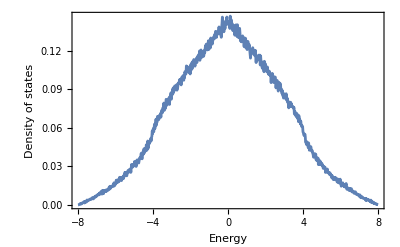

```mathematica
ListLinePlot[dos,Frame->True,FrameStyle->Black,FrameLabel->{"Energy","Density of states"},PlotRange->All]
```

Related Guides

HyperBloch Package

Related Tech Notes

## Metadata

### Categorization

Tech Note

PatrickMLenggenhager/HyperBloch

PatrickMLenggenhager`HyperBloch`

PatrickMLenggenhager/HyperBloch/tutorial/BasicUsage

### Keywords